```mathematica
Module[{xMin=-0.5,xMax=1.5,zMin=-0.5,zMax=0.5,Δ=0.1,
a,b,cl,cm,cpC,gAirfoil,gStreamPlot,gSurfaceCp,gFlowViz,ica,icb,id,plotLabel,rC,rF,rP,tuples,V,VMagC,V∞,x,xC,xCenterPressure,x0,z,z0,α},
(****** airfoil geometry *****)
id=1000c1+400+c3;
α=αD*Degree;
rP=DiscretizeAirfoil[id,nd];
gAirfoil=ListPlot[Transpose[Components[rP]],AspectRatio->Automatic,Axes->False,Frame->True,FrameLabel->{Style["x",Italic],Style["z",Italic]},FrameTicks->{Chop[Range[-1.2,1.6,0.2]],Chop[Range[-1.0,1.0,0.1]],None,Chop[Range[-1.0,1.0,0.1]]},ImageSize->500,Joined->True,PlotRange->{{-0.05,1.05},{-0.1,0.201}},RotateLabel->False];
(***** solve model *****)
{a,b,rC,VMagC}=PanelMethod[rP,α ];
xC=Components[rC][[1]];
cpC=1-VMagC^2;
{cl,cm}=ForceAndMoment[a,b,rP,α,rC];
xCenterPressure=-cm/cl;
(***** generate graphics *****)
plotLabel=Row[{"NACA ",If[c1≠0,StringJoin[Map[ToString,PadLeft[IntegerDigits[id=1000c1+400+c3], 4]]],StringJoin[Map[ToString,PadLeft[IntegerDigits[id=1000c1+c3], 4]]]]," Airfoil"}];
Switch[plot,
aero,
(***** plot surface pressure coefficient *****)
gSurfaceCp=ListPlot[Transpose[{xC,-cpC}],Frame->True,FrameLabel->{Style["x",Italic],"C_p"},FrameTicks->{Automatic,Transpose[{Range[-1,4,1],ToString/@(-Range[-1,4,1])}],None,None},ImageSize->500,PlotLabel->plotLabel,PlotRange->{{-0.05,1.05},{-1.1,4.1}},PlotStyle->PointSize[Large],RotateLabel->False,
Prolog->{Inset[Panel[Text@Grid[
{{Row[{"α = ",NumberForm[α/Degree,{3,2}],"°"}]},
{Row[{"C_ℓ = ",NumberForm[cl,{3,2}]}]},
{Row[{"C_m = ",NumberForm[cm,{3,2}]}]},
{Row[{"x_cp = ", NumberForm[xCenterPressure,{3,2}]}]}}
]],{.93,3.03}],Inset[ListPlot[Transpose[Components[rP]],AspectRatio->Automatic,Axes->False,Joined->True,Epilog->{EdgeForm[Black],Yellow,Disk[{xCenterPressure,0},.012]},Frame->False,PlotRange->{{0,1},Automatic}],{0,0},{0,0},1]}],
flowviz,
(***** stream plot *****)
V∞=UniformFlow[1,α];
z0=Range[zMin,zMax,Δ];
x0=Table[xMin+.05,{Length[z0]}];
tuples=Transpose[{x0,z0}];
rF={x,z};
{ica,icb}=ICVortexLinear[rF,rP];
V=V∞+ica.a+icb.b;
gStreamPlot=StreamPlot[V,{x,xMin,xMax},{z,zMin,zMax},AspectRatio->Automatic,FrameLabel->{Style["x",Italic],Style["z",Italic]},PlotLabel->plotLabel,StreamPoints->{tuples},RotateLabel->False,StreamScale->{Full,All,0.015}];
gFlowViz=Show[gStreamPlot,gAirfoil]
](*end switch*)
]
```

```mathematica
c4/.First@Solve[(0.2969-0.1260 -0.3516+0.2843-c4)==0,c4]//FullForm
```

```mathematica
yc[x_,c_:1]:=Piecewise[{{(m x)/p^2(2p-x/c), 0≤x≤p c}, {(m (c-x))/(1-p)^2(1-(2p-x/c)), p c≤x≤c}, {0, True}}]
yt[x_,c_:1]:=Chop[5t c(0.2969 √(x/c)-0.1260 x/c-0.3516(x/c)^2+0.2843(x/c)^3-0.1036(x/c)^4)]
```

```mathematica
yt[1]
```

```mathematica
Manipulate[{tt,Maximize[{yt[x]/.t->tt,0≤x≤1},{x}],yt[1]/.t->tt},{tt,0.001,0.20}]
```

```mathematica
yt[1]/.t->0.12
```

```mathematica
(D[yt[x],x]//FullSimplify)/.x->1
```

```mathematica
Plot[0.2969 √xx-0.1260 xx-0.3516(xx)^2+0.2843(xx)^3-0.10315(xx)^4,{xx,0,1.002},PlotRange->{{0,1.0020},{0,0.15}},AspectRatio->0.15/1.0020]
Plot[0.2969 √xx-0.1260 xx-0.3516(xx)^2+0.2843(xx)^3-0.10315(xx)^4,{xx,0,1.002},PlotRange->{{1,1.0020},{0,0.0005}},AspectRatio->0.0005/0.0020]
```

```mathematica
Series[0.2969 √xx-0.1260 xx-0.3516(xx)^2+0.2843(xx)^3-0.10315(xx)^4,{xx,1,10}]
```

```mathematica
Series[√(2p(1+ϵ-xx))+α1(1+ϵ-xx)+α2(1+ϵ-xx)^2+α3(1+ϵ-xx)^3+α4(1+ϵ-xx)^4,{xx,1,10}]
```

```mathematica
NSolve[
Table[
SeriesCoefficient[0.2969 √xx-0.1260 xx-0.3516(xx)^2+0.2843(xx)^3-0.1015(xx)^4,{xx,1,k}]==SeriesCoefficient[√(2p(1+ϵ-xx))+α1(1+ϵ-xx)+α2(1+ϵ-xx)^2+α3(1+ϵ-xx)^3,{xx,1,k}]
,{k,0,2}]~Join~{ϵ>0}
,{p,ϵ,α1,α2,α3},Reals]
```

```mathematica
Plot[{0.2969 √xx-0.1260 xx-0.3516(xx)^2+0.2843(xx)^3-0.1015(xx)^4,
√(2p(1+ϵ-xx))+α1(1+ϵ-xx)+α2(1+ϵ-xx)^2+α3(1+ϵ-xx)^3/.{p->0.0005860575512797173,ϵ->0.0050544107511712255,α1->-0.12491972188290168,α2->11.579398976610927,α3->12.21202728162769}
},{xx,1,1.002},PlotRange->{{1,1.0020},{0,0.0005}},AspectRatio->0.0005/0.0020]
```

```mathematica
√(2p(1+ϵ-xx))+α1(1+ϵ-xx)+α2(1+ϵ-xx)^2+α3(1+ϵ-xx)^3/.{p->0.0005860575512797173,ϵ->0.0050544107511712255,α1->-0.12491972188290168,α2->11.579398976610927,α3->12.21202728162769}
```

```mathematica
0.03423616658680458 √(1.0050544107511712-xx)-0.12491972188290168 (1.0050544107511712-xx)+11.579398976610927 (1.0050544107511712-xx)^2+12.21202728162769 (1.0050544107511712-xx)^3
```

```mathematica
yt0012[ξ_]:=5*0.12*Piecewise[{{0.2969 √ξ-0.1260 ξ-0.3516(ξ)^2+0.2843(ξ)^3-0.1015(ξ)^4, 0≤ξ≤1}, {0.00672100374755054 √(1.0014682552635628-ξ)+0.10945363951544834 (1.0014682552635628-ξ)+14.709681629928797 (1.0014682552635628-ξ)^2+15.534280059787614 (1.0014682552635628-ξ)^3, 1<ξ≤1.0014682552635628}, {0, True}}]
```

```mathematica
Plot[yt0012[ξ],{ξ,0,1.0014682552635628}]
```

```mathematica
sol1=NDSolve[{
x[ξ,0]==ξ,
y[ξ,0]==yt0012[ξ],
x[0,η]==-η,
y[0,η]==0,
x[1,η]==4/5 η+1,
y[1,η]==0,
x[ξ,5]==Piecewise[{{-5/(√(5^2+(2ξ-5)^2)), -5≤ξ<-2.5}, {(2ξ)/(√(5^2+(2ξ-5)^2)), -2.5≤ξ<0}, {2ξ, 0≤ξ≤2.5}, {5, 2.5<ξ≤5}, {Null, True}}],
y[ξ,5]==Piecewise[{{(2ξ-5)/(√(5^2+(2ξ-5)^2)), -5≤ξ<-2.5}, {5/(√(5^2+(2ξ)^2)), -2.5≤ξ<0}, {5, 0≤ξ≤2.5}, {5-2ξ, 2.5<ξ≤5}, {Null, True}}],
D[x[ξ,η], ξ,ξ]+D[x[ξ,η], η,η]==0,D[y[ξ,η], ξ,ξ]+D[y[ξ,η], η,η]==0},{x,y},
{ξ,0,1},{η,0,5}]
```

```mathematica
sol1=NDSolve[Inactivate[{
x[ξ,0]==ξ,
y[ξ,0]==yt0012[ξ],
x[0,η]==-η,
y[0,η]==0,
x[1,η]==4/5 η+1,
y[1,η]==0,
x[ξ,5]==Piecewise[{{-5/(√(5^2+(2ξ-5)^2)), -5≤ξ<-2.5}, {(2ξ)/(√(5^2+(2ξ)^2)), -2.5≤ξ<0}, {2ξ, 0≤ξ≤2.5}, {5, 2.5<ξ≤5}, {Null, True}}],
y[ξ,5]==Piecewise[{{(2ξ-5)/(√(5^2+(2ξ-5)^2)), -5≤ξ<-2.5}, {5/(√(5^2+(2ξ)^2)), -2.5≤ξ<0}, {5, 0≤ξ≤2.5}, {5-2ξ, 2.5<ξ≤5}, {Null, True}}],
((D[x[ξ,η], η])^2+(D[y[ξ,η], η])^2)D[x[ξ,η], ξ,ξ]-2(D[x[ξ,η], ξ]D[x[ξ,η], η]+D[y[ξ,η], ξ]D[y[ξ,η], η])D[x[ξ,η], ξ,η]+((D[x[ξ,η], ξ])^2+(D[y[ξ,η], ξ])^2)D[x[ξ,η], η,η]==0,
((D[x[ξ,η], η])^2+(D[y[ξ,η], η])^2)D[y[ξ,η], ξ,ξ]-2(D[x[ξ,η], ξ]D[x[ξ,η], η]+D[y[ξ,η], ξ]D[y[ξ,η], η])D[y[ξ,η], ξ,η]+((D[x[ξ,η], ξ])^2+(D[y[ξ,η], ξ])^2)D[y[ξ,η], η,η]==0
},Dt],{x,y},{ξ,0,1},{η,0,5}]
```

```mathematica
sol1=NDSolve[Inactivate[{
x[ξ,0]==ξ,
y[ξ,0]==yt0012[ξ],
x[0,η]==-η,
y[0,η]==0,
x[1,η]==4/5 η+1,
y[1,η]==0,
x[ξ,5]==Piecewise[{{-5/(√(5^2+(2ξ-5)^2)), -5≤ξ<-2.5}, {(2ξ)/(√(5^2+(2ξ)^2)), -2.5≤ξ<0}, {2ξ, 0≤ξ≤2.5}, {5, 2.5<ξ≤5}, {Null, True}}],
y[ξ,5]==Piecewise[{{(2ξ-5)/(√(5^2+(2ξ-5)^2)), -5≤ξ<-2.5}, {5/(√(5^2+(2ξ)^2)), -2.5≤ξ<0}, {5, 0≤ξ≤2.5}, {5-2ξ, 2.5<ξ≤5}, {Null, True}}],
((D[x[ξ,η], η])^2+(D[y[ξ,η], η])^2)D[x[ξ,η], ξ,ξ]-2(D[x[ξ,η], ξ]D[x[ξ,η], η]+D[y[ξ,η], ξ]D[y[ξ,η], η])D[x[ξ,η], ξ,η]+((D[x[ξ,η], ξ])^2+(D[y[ξ,η], ξ])^2)D[x[ξ,η], η,η]==0,
((D[x[ξ,η], η])^2+(D[y[ξ,η], η])^2)D[y[ξ,η], ξ,ξ]-2(D[x[ξ,η], ξ]D[x[ξ,η], η]+D[y[ξ,η], ξ]D[y[ξ,η], η])D[y[ξ,η], ξ,η]+((D[x[ξ,η], ξ])^2+(D[y[ξ,η], ξ])^2)D[y[ξ,η], η,η]==0
},Dt],{x,y},{ξ,η}∈Rectangle[{0,0},{1,5}]]
```

```mathematica
DensityPlot[x[ξ,η]/.sol1,{ξ,0,1},{η,0,5}]
```

```mathematica
ParametricPlot[Table[{x[ξ,η],y[ξ,η]}/.sol1,{η,{5}}],{ξ,0,1},PlotRange->All,AspectRatio->Automatic]
```

```mathematica
Mesh
```

```mathematica
RegionDifference[Disk[{0,0},15],Disk[{0,0},2]]
```

```mathematica
RegionDifference[RegionUnion[Disk[{0,0},5],Rectangle[{0,-5},{5,5}]],ImplicitRegion[Abs[y]<yt0012[x],{{x,0,1.1},{y,-1,1}}]]//Region
```

```mathematica
DiscretizeRegion[ImplicitRegion[Abs[y]≥yt0012[x]&&-5≤x≤5&&-5≤y≤5,{{x,-5,5},{y,-5,5}}]]
```

```mathematica
Region
```

```mathematica
Region[ImplicitRegion[Abs[y]<yt0012[x],{{x,0,1.1},{y,-1,1}}],PlotRange->All]
```

```mathematica
RegionUnion[Disk[{0,0},5],Rectangle[{0,-5},{5,5}]]//Region
```

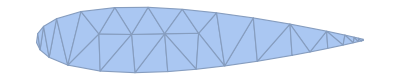
```mathematica
DiscretizeRegion[RegionDifference[RegionUnion[Disk[{0,0},5],Rectangle[{0,-5},{5,5}]],-Graphics-],PrecisionGoal->5]
```

1+1